```mathematica
For[i=13,i≤Prime[15],i++,Print[i]]
```

13

14

15

16

17

18

19

20

21

22

23

24

25

26

27

28

29

30

31

32

33

34

35

36

37

38

39

40

41

42

43

44

45

46

47

```mathematica
For[i=13,i≤Prime[15],i+=3,Print[i]]
```

13

16

19

22

25

28

31

34

37

40

43

46

```mathematica
j=-2;
```

```mathematica
While[j≤9,Print[j];j+=3]
```

-2

1

4

7

```mathematica
k=5;
```

```mathematica
m=Table[0,{i,k},{j,k}];
```

```mathematica
Do[m[[i]][[1]]=i Subscript[b, i],{i,k}];
```

```mathematica
Do[m[[i]][[j]]= Subscript[b, i+1-j],{j,2,k},{i,j,k}];
```

```mathematica
Do[m[[i]][[i+1]]=1,{i,1,k-1}];
```

```mathematica
MatrixForm[m]
```

(b_1 | 1 | 0 | 0 | 0
2 b_2 | b_1 | 1 | 0 | 0
3 b_3 | b_2 | b_1 | 1 | 0
4 b_4 | b_3 | b_2 | b_1 | 1
5 b_5 | b_4 | b_3 | b_2 | b_1)

```mathematica
Range[97]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97}

```mathematica
a=Range[97];
```

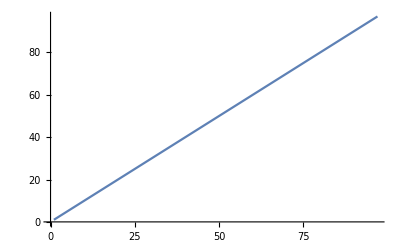

```mathematica
ListLinePlot[a]
```

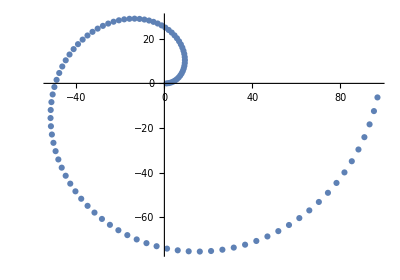

```mathematica
ListPolarPlot[a]
```